```mathematica
Get["/home/physic/Downloads/melt/melt.m"](*cargando melt*)
LoadPlotStyling[]
```

```mathematica
SetDirectory["/home/physic/Desktop/magister/tesis/res"];
```

# Hamiltoniano

```mathematica
(*Construccion de las respectivas bases de excitones*)
Clear[delta,v,Xb1,Xb2,Xd1,Xd2,be,Xbp,Xbm,Xdp,Xdm,ds]
(**)
delta[i_,j_]:=delta[i,j]=KroneckerDelta[i,j]
v=Table[delta[0,i],{i,0,4}];
(*--estados de excitones desnudos*)
Xb1=Table[delta[1,i],{i,0,4}];
Xb2=Table[delta[2,i],{i,0,4}];
Xd1=Table[delta[3,i],{i,0,4}];
Xd2=Table[delta[4,i],{i,0,4}];
(*base desnuda*)
be={v,Xb1,Xb2,Xd1,Xd2};
(*--estados de excitones vestidos*)
Xbp=Table[delta[1,i]+delta[2,i],{i,0,4}]/Sqrt[2]; 
Xbm=Table[delta[1,i]-delta[2,i],{i,0,4}]/Sqrt[2];
Xdp=Table[delta[3,i]+delta[4,i],{i,0,4}]/Sqrt[2];
Xdm=Table[delta[3,i]-delta[4,i],{i,0,4}]/Sqrt[2];
(*base vestida*)
ds={v,Xbp,Xbm,Xdp,Xdm};
```

```mathematica
Clear[s,σ,c]
(*operador vestido*)
s[i_,j_]:=s[i,j]=SparseArray[Table[Sum[
ds[[k+1]].be[[i+1]]be[[j+1]].ds[[l+1]]delta[m+1,k+1]delta[l+1,n+1],
{k,0,4},{l,0,4}],{m,0,4},{n,0,4}]]
(*operadores en la base acoplada*)
σ[i_,j_,n_]:=σ[i,j,n]=kron[Eye[n+1],s[i,j]]
c[n_]:=c[n]=SparseArray[kron[
Table[√j delta[i,j-1],{i,0,n},{j,0,n}],Eye[5]]]
```

```mathematica
Clear[cav,qdi,qd,lasi,efi,efidag,βp,βm,βe,βh,magi,mag,H]
(*sub-Hamiltonianos*)
cav[n_]:=cav[n]=ωc*c[n]ᵀ.c[n]
qdi[n_]:=qdi[n]=(δb*σ[1,2,n]+δd*σ[3,4,n])/2;
qd[Δ_,n_]:=qd[Δ,n]=
Δ Sum[σ[j,j,n],{j,2}]+(Δ-δ0)Sum[σ[j,j,n],{j,3,4}]+qdi[n]+qdi[n]ᵀ
lasi[n_]:=lasi[n]=Ω1*σ[0,1,n]+Ω2*σ[0,2,n]
efi[n_]:=efi[n]=(gbd((1+ⅈ)Sum[σ[1,j,n],{j,3,4}]+(1-ⅈ)Sum[σ[2,j,n],{j,3,4}])/Sqrt[2]
+gbb(ⅈ(σ[1,2,n]-σ[2,1,n]))).(c[n]ᵀ+c[n])
efidag[n_]:=SparseArray[Simplify[Normal[efi[n]†],Element[gbb|gbd,Reals]]]
ef[n_]:=gbb*Sum[σ[j,j,n],{j,2}].(c[n]ᵀ+c[n])+efi[n]+efidag[n]
βp[B_,θ_]:=βp[B,θ]=μB(gez+ghz)*B*Sin[θ]/2
βm[B_,θ_]:=βm[B,θ]=μB(gez-ghz)*B*Sin[θ]/2
βe[B_,θ_]:=βe[B,θ]=μB*gex*B*Cos[θ]/2
βh[B_,θ_]:=βh[B,θ]=μB*ghx*B*Cos[θ]/2
magi[B_,θ_,n_]:=magi[B,θ,n]=
βe[B,θ](σ[1,3,n]+σ[2,4,n])+βh[B,θ](σ[1,4,n]+σ[2,3,n])
mag[B_,θ_,n_]:=mag[B,θ,n]=
βp[B,θ](σ[1,1,n]-σ[2,2,n])+βm[B,θ](σ[4,4,n]-σ[3,3,n])+α B^2 Sum[σ[j,j,n],{j,4}]+magi[B,θ,n]+magi[B,θ,n]ᵀ
(*-Hamiltoniano*)
H[Δ_,B_,θ_,n_]:=H[Δ,B,θ,n]=
SparseArray[cav[n]+qd[Δ,n]+lasi[n]+lasi[n]ᵀ+ef[n]+mag[B,θ,n]]
d[n_]:=Length[H[0,0,0,n]]
```

## simbólico

## Elementos de transicion

```mathematica
H[Δ,0,θ,2]//mf;
%//ArrayRules//FullSimplify
```

(0 | Ω1/(√2)+Ω2/(√2) | Ω1/(√2)-Ω2/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
Ω1/(√2)+Ω2/(√2) | Δ+δb/2 | 0 | 0 | 0 | 0 | gbb | -2 ⅈ gbb | √2 gbd | 0 | 0 | 0 | 0 | 0 | 0
Ω1/(√2)-Ω2/(√2) | 0 | Δ-δb/2 | 0 | 0 | 0 | 2 ⅈ gbb | gbb | ⅈ √2 gbd | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δ-δ0+δd/2 | 0 | 0 | √2 gbd | -ⅈ √2 gbd | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δ-δ0-δd/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ωc | Ω1/(√2)+Ω2/(√2) | Ω1/(√2)-Ω2/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | gbb | -2 ⅈ gbb | √2 gbd | 0 | Ω1/(√2)+Ω2/(√2) | Δ+δb/2+ωc | 0 | 0 | 0 | 0 | √2 gbb | -2 ⅈ √2 gbb | 2 gbd | 0
0 | 2 ⅈ gbb | gbb | ⅈ √2 gbd | 0 | Ω1/(√2)-Ω2/(√2) | 0 | Δ-δb/2+ωc | 0 | 0 | 0 | 2 ⅈ √2 gbb | √2 gbb | 2 ⅈ gbd | 0
0 | √2 gbd | -ⅈ √2 gbd | 0 | 0 | 0 | 0 | 0 | Δ-δ0+δd/2+ωc | 0 | 0 | 2 gbd | -2 ⅈ gbd | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ-δ0-δd/2+ωc | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 ωc | Ω1/(√2)+Ω2/(√2) | Ω1/(√2)-Ω2/(√2) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | √2 gbb | -2 ⅈ √2 gbb | 2 gbd | 0 | Ω1/(√2)+Ω2/(√2) | Δ+δb/2+2 ωc | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 ⅈ √2 gbb | √2 gbb | 2 ⅈ gbd | 0 | Ω1/(√2)-Ω2/(√2) | 0 | Δ-δb/2+2 ωc | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 gbd | -2 ⅈ gbd | 0 | 0 | 0 | 0 | 0 | Δ-δ0+δd/2+2 ωc | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δ-δ0-δd/2+2 ωc)

{{1,2}→(Ω1+Ω2)/(√2),{1,3}→(Ω1-Ω2)/(√2),{2,1}→(Ω1+Ω2)/(√2),{2,2}→Δ+δb/2,{2,7}→gbb,{2,8}→-2 ⅈ gbb,{2,9}→√2 gbd,{3,1}→(Ω1-Ω2)/(√2),{3,3}→Δ-δb/2,{3,7}→2 ⅈ gbb,{3,8}→gbb,{3,9}→ⅈ √2 gbd,{4,4}→Δ-δ0+δd/2,{4,7}→√2 gbd,{4,8}→-ⅈ √2 gbd,{5,5}→Δ-δ0-δd/2,{6,6}→ωc,{6,7}→(Ω1+Ω2)/(√2),{6,8}→(Ω1-Ω2)/(√2),{7,2}→gbb,{7,3}→-2 ⅈ gbb,{7,4}→√2 gbd,{7,6}→(Ω1+Ω2)/(√2),{7,7}→Δ+δb/2+ωc,{7,12}→√2 gbb,{7,13}→-2 ⅈ √2 gbb,{7,14}→2 gbd,{8,2}→2 ⅈ gbb,{8,3}→gbb,{8,4}→ⅈ √2 gbd,{8,6}→(Ω1-Ω2)/(√2),{8,8}→Δ-δb/2+ωc,{8,12}→2 ⅈ √2 gbb,{8,13}→√2 gbb,{8,14}→2 ⅈ gbd,{9,2}→√2 gbd,{9,3}→-ⅈ √2 gbd,{9,9}→Δ-δ0+δd/2+ωc,{9,12}→2 gbd,{9,13}→-2 ⅈ gbd,{10,10}→Δ-δ0-δd/2+ωc,{11,11}→2 ωc,{11,12}→(Ω1+Ω2)/(√2),{11,13}→(Ω1-Ω2)/(√2),{12,7}→√2 gbb,{12,8}→-2 ⅈ √2 gbb,{12,9}→2 gbd,{12,11}→(Ω1+Ω2)/(√2),{12,12}→Δ+δb/2+2 ωc,{13,7}→2 ⅈ √2 gbb,{13,8}→√2 gbb,{13,9}→2 ⅈ gbd,{13,11}→(Ω1-Ω2)/(√2),{13,13}→Δ-δb/2+2 ωc,{14,7}→2 gbd,{14,8}→-2 ⅈ gbd,{14,14}→Δ-δ0+δd/2+2 ωc,{15,15}→Δ-δ0-δd/2+2 ωc,{_,_}→0}

## Transicion del estado vacio al estado oscuro simetrico con 2 fonones

Todas las transiciones relacionadas con el estado 14=X_(d+),2
Los estados involucrados son: 1=v,0, 2=X_(b+),0, 3=X_(b-),0, 4=X_(d+),0, 6=v,0, 7=X_(b+),1, 8=X_(b-),1, 11=v,2, 12=X_(b+),2, 14=X_(d+),2, 15=X_(d-),2, 17=X_(b+),3 y 18=X_(b-),3

{2,1}→(Ω1+Ω2)/(√2),
{3,1}→(Ω1-Ω2)/(√2),{3,2}→1/2 B (gez+ghz) μB Sin[θ]
{4,2}→1/2 B (gex+ghx) μB Cos[θ]
{7,2}→2 gbb,{7,3}→-2 ⅈ gbb,{7,4}→√2 gbd,{7,6}→(Ω1+Ω2)/(√2)
{8,2}→2 ⅈ gbb,{8,3}→2 gbb,{8,4}→ⅈ √2 gbd,{8,6}→(Ω1-Ω2)/(√2),{8,7}→1/2 B (gez+ghz) μB Sin[θ]
{12,7}→2 √2 gbb,{12,8}→-2 ⅈ √2 gbb,{12,9}→2 gbd,{12,11}→(Ω1+Ω2)/(√2)
{14,7}→2 gbd,{14,8}→-2 ⅈ gbd,{14,12}→1/2 B (gex+ghx) μB Cos[θ]
{15,14}→1/2 B (-gez+ghz) μB Sin[θ]
{17,14}→√6 gbd
{18,14}→ⅈ √6 gbd

### Hamiltonianos reducidos

```mathematica
Clear[Hred]
Hred[Δ_]:=Block[{list0={1,2,3,7,8,14,17,18},list={1,2,3,4,6,7,8,9,11,12,14,15,17,18}},
Table[H[Δ,0,0,4][[i,j]],{i,list0},{j,list0}]]//FullSimplify
```

```mathematica
Hred[Δ]//mf;
```

(0 | (Ω1+Ω2)/(√2) | (Ω1-Ω2)/(√2) | 0 | 0 | 0 | 0 | 0
(Ω1+Ω2)/(√2) | Δ+δb/2 | 0 | 2 gbb | -2 ⅈ gbb | 0 | 0 | 0
(Ω1-Ω2)/(√2) | 0 | Δ-δb/2 | 2 ⅈ gbb | 2 gbb | 0 | 0 | 0
0 | 2 gbb | -2 ⅈ gbb | Δ+δb/2+ωc | 0 | 2 gbd | 0 | 0
0 | 2 ⅈ gbb | 2 gbb | 0 | Δ-δb/2+ωc | 2 ⅈ gbd | 0 | 0
0 | 0 | 0 | 2 gbd | -2 ⅈ gbd | Δ-δ0+δd/2+2 ωc | √6 gbd | -ⅈ √6 gbd
0 | 0 | 0 | 0 | 0 | √6 gbd | Δ+δb/2+3 ωc | 0
0 | 0 | 0 | 0 | 0 | ⅈ √6 gbd | 0 | Δ-δb/2+3 ωc)

```mathematica
Table[HH[[i,j]],{i,{1,2,3,7,8,14}},{j,{1,2,3,7,8,14}}]//mf;
```

(0 | Ω1/(√2)+Ω2/(√2) | Ω1/(√2)-Ω2/(√2) | 0 | 0 | 0
Ω1/(√2)+Ω2/(√2) | Δ+δb/2 | 0 | 2 gbb | -2 ⅈ gbb | 0
Ω1/(√2)-Ω2/(√2) | 0 | Δ-δb/2 | 2 ⅈ gbb | 2 gbb | 0
0 | 2 gbb | -2 ⅈ gbb | Δ+δb/2+ωc | 0 | 2 gbd
0 | 2 ⅈ gbb | 2 gbb | 0 | Δ-δb/2+ωc | 2 ⅈ gbd
0 | 0 | 0 | 2 gbd | -2 ⅈ gbd | Δ-δ0+δd/2+2 ωc)

```mathematica
h=Table[HH[[i,j]],{i,{1,2,7,14}},{j,{1,2,7,14}}]//mf;
```

(0 | Ω1/(√2)+Ω2/(√2) | 0 | 0
Ω1/(√2)+Ω2/(√2) | Δ+δb/2 | 2 gbb | 0
0 | 2 gbb | Δ+δb/2+ωc | 2 gbd
0 | 0 | 2 gbd | Δ-δ0+δd/2+2 ωc)

```mathematica
hh=Table[HH[[i,j]],{i,{2,7}},{j,{2,7}}]//mf;
Eigenvalues[hh]
FullSimplify[Map[#/(√(#.#))&,Eigenvectors[hh]],gbb>0&&ωc>0]
```

(Δ+δb/2 | 2 gbb
2 gbb | Δ+δb/2+ωc)

{1/2 (2 Δ+δb+ωc-√(16 gbb^2+ωc^2)),1/2 (2 Δ+δb+ωc+√(16 gbb^2+ωc^2))}

{{(-ωc-√(16 gbb^2+ωc^2))/(√(32 gbb^2+2 ωc (ωc+√(16 gbb^2+ωc^2)))),1/(√(2+(ωc (ωc+√(16 gbb^2+ωc^2)))/(8 gbb^2)))},{(-ωc+√(16 gbb^2+ωc^2))/(√(32 gbb^2+2 ωc (ωc-√(16 gbb^2+ωc^2)))),(√(1+ωc/(√(16 gbb^2+ωc^2))))/(√2)}}

#### Anticruce y minimo con Hamiltonianos reducidos

```mathematica
eval=Eigenvalues[Hred[Δ],6];
```

```mathematica
param1={ωc->1.0,δ0->0.04,δb->0.018,δd->0.005,Ω1->0.082,Ω2->0.0,gbb->0.02,gbd->gbb,ghx->-0.35,ghz->-2.2,gex->-0.65,gez->-0.8,α->0.02,μB->0.0579};
```

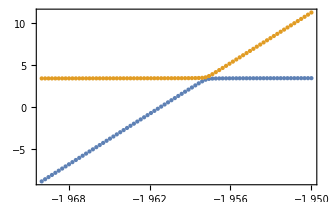

```mathematica
dat[i_]:=Table[{Δ,1000*eval[[i]]//.param1},{Δ,linspace[-1.97,-1.95,80]}]
ListPlot[{dat[5],dat[6]},PlotRange->All]
```

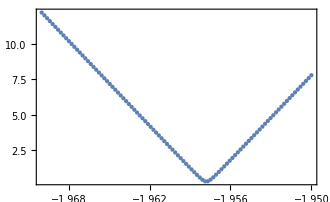

```mathematica
Clear[dat]
dat=Table[{Δ,1000*resta//.param1},{Δ,linspace[-1.97,-1.95,100]}];
ListPlot[{dat},PlotRange->All]
```

```mathematica
NMinimize[resta//.param1,Δ]
```

{0.000278019,{Δ→-1.95779}}

```mathematica
resta=eval[[6]]-eval[[5]]//FullSimplify;
```

```mathematica
Hredred=Block[{list0={2,3,7,8}},
Table[H[Δ,0,0,4][[i,j]],{i,list0},{j,list0}]]//FullSimplify//mf;
```

(Δ+δb/2 | 0 | 2 gbb | -2 ⅈ gbb
0 | Δ-δb/2 | 2 ⅈ gbb | 2 gbb
2 gbb | -2 ⅈ gbb | Δ+δb/2+ωc | 0
2 ⅈ gbb | 2 gbb | 0 | Δ-δb/2+ωc)

```mathematica
eval2=Eigenvalues[Hredred]
```

{1/2 (2 Δ+ωc-√(32 gbb^2+δb^2+ωc^2-2 √(256 gbb^4+16 gbb^2 δb^2+δb^2 ωc^2))),1/2 (2 Δ+ωc+√(32 gbb^2+δb^2+ωc^2-2 √(256 gbb^4+16 gbb^2 δb^2+δb^2 ωc^2))),1/2 (2 Δ+ωc-√(32 gbb^2+δb^2+ωc^2+2 √(256 gbb^4+16 gbb^2 δb^2+δb^2 ωc^2))),1/2 (2 Δ+ωc+√(32 gbb^2+δb^2+ωc^2+2 √(256 gbb^4+16 gbb^2 δb^2+δb^2 ωc^2)))}

```mathematica
Clear[ℰ]
ℰ[Δ_]:=ℰ[Δ]=Eigvals[Hred[Δ]//.param1]*1000
```

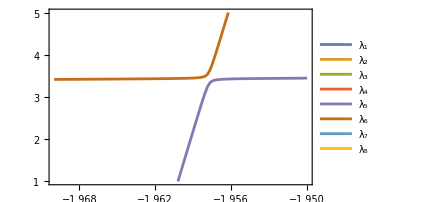

```mathematica
Clear[dat]
dat[i_]:=Table[{Δ,ℰ[Δ][[i]]},{Δ,linspace[-1.97,-1.95,100]}]
ListPlot[Table[dat[i],{i,Length[Hred[0]]}],PlotLegends->{Table[Subscript[λ, i],{i,Length[Hred[0]]}]},PlotRange->{1,5},Joined->True]
```

```mathematica
𝒮[Δ_]:=Eigvecs[Hred[Δ]//.param1]
```

```mathematica
Module[{resta,x0=-1.97,xf=-1.95,ϵ=0.00001,h,φ=(1+√5)/2,x1,x2},
resta[Δ_]:=ℰ[Δ][[6]]-ℰ[Δ][[5]];
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[resta[x1]>=resta[x2],x0=x1,xf=x2];];(xf+x0)/2]
```

-1.95778

```mathematica
(𝒮[-1.95778][[All,6]])^2//Chop//Abs
```

{0.489702,0.000470914,0.000462014,0.000972706,0.000936953,0.505207,0.00110472,0.00114369}

```mathematica
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[ℰrest[i,x1,B,θ,n]>=ℰrest[i,x2,B,θ,n],x0=x1,xf=x2];];(xf+x0)/2.0]
```

## numérico

```mathematica
(* parametros del Hamiltoniano*)
{ωc=1.0}; (*cavidad*)
{δ0=0.04,δb=0.018,δd=0.005}; (*punto cuantico*)
{Ω1=0.082,Ω2=0.0};(*bombeo coherente semiclasico*)
{gbb=0.02,gbd=gbb}; (*interaccion electron-fonon*)
(*--campo magnetico*)
{ghx=-0.35,ghz=-2.2,gex=-0.65,gez=-0.8,α=0.02,μB=0.0579};
```

```mathematica
Clear[v0,esys,ℰ,𝒮,hfd,ψ]
(*descomposicion espectral*)
v0[n_]:=v0[n]=Table[delta[i,1],{i,Length[c[n]]}];
Xdp2[n_]:=Xdp2[n]=Table[delta[i,14],{i,Length[c[n]]}];
esys[Δ_,B_,θ_,n_]:=esys[Δ,B,θ,n]=
Transpose[Sort[Transpose[Eigensystem[H[Δ,B,θ,n],Method->"Banded"]]]]
ℰ[Δ_,B_,θ_,n_]:=ℰ[Δ,B,θ,n]=Chop[esys[Δ,B,θ,n][[1]]*1000]
𝒮[Δ_,B_,θ_,n_]:=𝒮[Δ,B,θ,n]=Chop[esys[Δ,B,θ,n][[2]]]
(*coeficientes de Hopfield*)
hfd[i_,Δ_,B_,θ_,n_]:=hfd[i,Δ,B,θ,n]=Abs[𝒮[Δ,B,θ,n][[i[[1]],i[[2]]]]]^2
(*dinamica unitaria*)
ψ[t_,Δ_,B_,θ_,n_]:=ψ[t,Δ,B,θ,n]=SparseArray[Chop[MatrixExp[-ⅈ*t*H[Δ,B,θ,n],v0[n]]]]
```

```mathematica
Clear[ℰrest,linticks]
(*resta de energias*)
ℰrest[i_,Δ_,B_,θ_,n_]:=ℰrest[i,Δ,B,θ,n]=ℰ[Δ,B,θ,n][[i+1]]-ℰ[Δ,B,θ,n][[i]]
(*personalizando ticks*)
linticks[i_,f_,δ_,sub_:4,ts_:0.8,label_:1]:=
Flatten[Table[
Join[
{{k,If[label==1,ToString[k],""],ts{0.026,0}}},
Table[{N[n/sub δ +k],"",ts{0.012,0}},{n,1,sub}]
]
,{k,i,f,δ}],1]
```

```mathematica
leyenda[labels_]:=LineLegend[Automatic,labels,LabelStyle->{FontFamily->"Times",FontSize->12},LegendLayout->{"Column",1},LegendMarkerSize->{12,2},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray,Background->Lighter[Gray,0.9]]&)]
```

## Vladimir

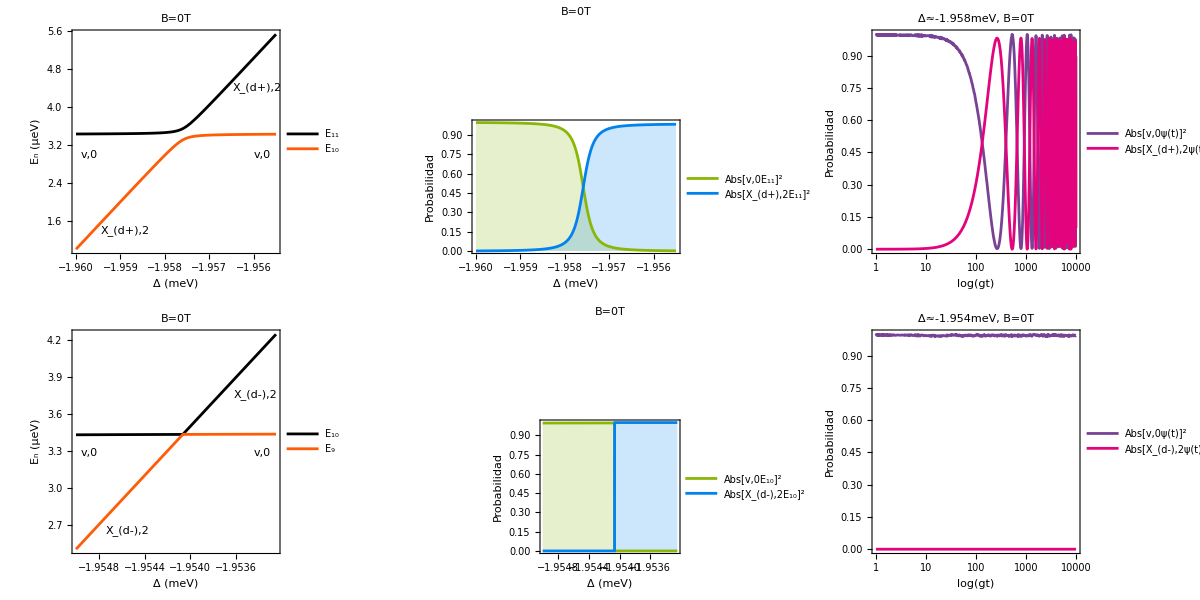

```mathematica
Module[{n=5,datψ,E11E10B0θ0,h11B0θ0,ψ14B0θ0,E10E9B0θ0,h10B0θ0,ψ15B0θ0,B=0,θ=0},
(*Vladimir*)
E11E10B0θ0=Plot[{ℰ[Δ,B,θ,n][[11]],ℰ[Δ,B,θ,n][[10]]},{Δ,-1.960,-1.9555},PlotLegends->legend[{"E_11","E_10"},{0.14,0.79},FontSize->12,LegendMarkerSize->12],PlotStyle->COLORLIST,FrameLabel->{"Δ (meV)","E_n (μeV)"},
Epilog->{Inset["v,0",{-1.9597,3.0}],Inset["v,0",{-1.9558,3.0}],Inset["X_(d+),2",{-1.9589,1.40}],Inset["X_(d+),2",{-1.95593,4.40}]},PlotLabel->Row[{"B=",NumberForm[B,3],"T"}],PlotStyle->{COLORLIST[[1]],COLORLIST[[2]]}];
h11B0θ0=Plot[{hfd[{11,1},Δ,B,θ,n],hfd[{11,14},Δ,B,θ,n]},{Δ,-1.960,-1.9555},PlotLegends->legend[{Abs["v,0E_11"]^2,Abs["X_(d+),2E_11"]^2},{0.23,0.5},FontSize->12,LegendMarkerSize->12],FrameLabel->{"Δ (meV)","Probabilidad"},
Epilog->{Inset["v,0",{-1.9597,3.0}],Inset["v,0",{-1.9558,3.0}],Inset["X_(d+),2",{-1.9589,1.40}],Inset["X_+,2",{-1.95593,4.40}]},PlotLabel->Row[{"B=",NumberForm[B,3],"T"}],Filling->Bottom,PlotStyle->{COLORLIST[[3]],COLORLIST[[4]]}];
Module[{Δ},Δ=-1.9576;
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ,B,θ,n][[i]]]^2},{t,logspace[0,4,800]}];
ψ14B0θ0=ListLogLinearPlot[{datψ[1],datψ[14]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,4,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->legend[{Abs["v,0ψ(t)"]^2,Abs["X_(d+),2ψ(t)"]^2},{0.25,0.5},FontSize->12,LegendMarkerSize->12],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",NumberForm[B,3],"T"}],PlotStyle->{COLORLIST[[5]],COLORLIST[[6]]}];
];
(*transicion prohibida*)
E10E9B0θ0=Plot[{ℰ[Δ,B,θ,n][[10]],ℰ[Δ,B,θ,n][[9]]},{Δ,-1.955,-1.95325},PlotLegends->legend[{"E_10","E_9"},{0.15,0.77},FontSize->12,LegendMarkerSize->12],PlotStyle->COLORLIST,FrameLabel->{"Δ (meV)","E_n (μeV)"},
Epilog->{Inset["v,0",{-1.95488,3.28}],Inset["v,0",{-1.95337,3.28}],Inset["X_(d-),2",{-1.95455,2.65}],Inset["X_(d-),2",{-1.95343,3.76}]},PlotLabel->Row[{"B=",NumberForm[B,3],"T"}],PlotStyle->{COLORLIST[[1]],COLORLIST[[2]]}];
h10B0θ0=Plot[{hfd[{10,1},Δ,B,θ,n],hfd[{10,15},Δ,B,θ,n]},{Δ,-1.955,-1.95325},PlotLegends->legend[{Abs["v,0E_10"]^2,Abs["X_(d-),2E_10"]^2},{0.23,0.5},FontSize->12,LegendMarkerSize->12],FrameLabel->{"Δ (meV)","Probabilidad"},
Epilog->{Inset["v,0",{-1.9597,3.0}],Inset["v,0",{-1.9558,3.0}],Inset["X_(d+),2",{-1.9589,1.40}],Inset["X_+,2",{-1.95593,4.40}]},PlotLabel->Row[{"B=",NumberForm[B,3],"T"}],Filling->Bottom,PlotStyle->{COLORLIST[[3]],COLORLIST[[4]]}];
Module[{Δ},Δ=-1.9541;
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ,B,θ,n][[i]]]^2},{t,logspace[0,4,400]}];
ψ15B0θ0=ListLogLinearPlot[{datψ[1],datψ[15]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,4,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->legend[{Abs["v,0ψ(t)"]^2,Abs["X_(d-),2ψ(t)"]^2},{0.25,0.5},FontSize->12,LegendMarkerSize->12],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",NumberForm[B,3],"T"}],PlotStyle->{COLORLIST[[5]],COLORLIST[[6]]}];
];
Export["E11E10B0θ0.pdf",E11E10B0θ0];
Export["h11B0θ0.pdf",h11B0θ0];
Export["ψ14B0θ0.pdf",ψ14B0θ0];
Export["E10E9B0θ0.pdf",E10E9B0θ0];
Export["h10B0θ0.pdf",h10B0θ0];
Export["ψ15B0θ0.pdf",ψ15B0θ0];
Grid[{{E11E10B0θ0,h11B0θ0,ψ14B0θ0},{E10E9B0θ0,h10B0θ0,ψ15B0θ0}}]
]
```

## Configuración de Voigt

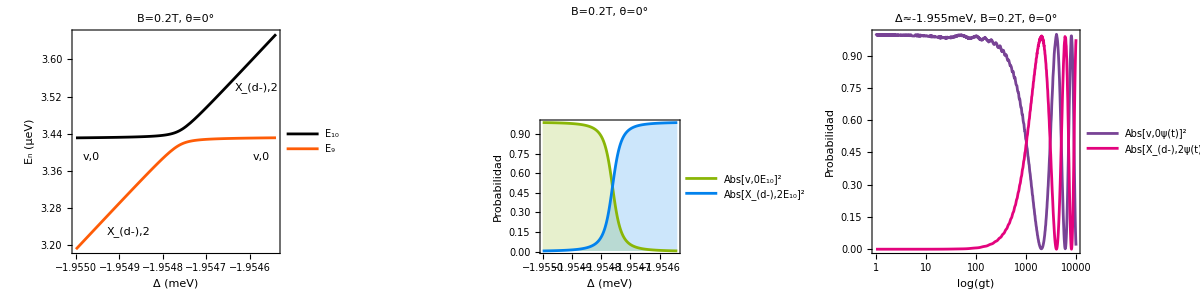

```mathematica
Module[{n=5,datψ,E10E9B02θ0,h10B02θ0,ψ15B02θ0,B=0.2,θ=0},
(*activacion de la nueva transicion*)
E10E9B02θ0=Plot[{ℰ[Δ,B,θ,n][[10]],ℰ[Δ,B,θ,n][[9]]},{Δ,-1.955,-1.95454},PlotLegends->legend[{"E_10","E_9"},{0.15,0.77},FontSize->12,LegendMarkerSize->12],PlotStyle->COLORLIST,FrameLabel->{"Δ (meV)","E_n (μeV)"},
Epilog->{Inset["v,0",{-1.954965,3.39}],Inset["v,0",{-1.954575,3.39}],Inset["X_(d-),2",{-1.95488,3.23}],Inset["X_(d-),2",{-1.954584,3.54}]},PlotLabel->Row[{"B=",B,"T, θ=",θ,"°"}],PlotStyle->{COLORLIST[[1]],COLORLIST[[2]]}];
h10B02θ0=Plot[{hfd[{10,1},Δ,B,θ,n],hfd[{10,15},Δ,B,θ,n]},{Δ,-1.955,-1.95454},PlotLegends->legend[{Abs["v,0E_10"]^2,Abs["X_(d-),2E_10"]^2},{0.23,0.5},FontSize->12,LegendMarkerSize->12],FrameLabel->{"Δ (meV)","Probabilidad"},
Epilog->{Inset["v,0",{-1.9597,3.0}],Inset["v,0",{-1.9558,3.0}],Inset["X_(d+),2",{-1.9589,1.40}],Inset["X_+,2",{-1.95593,4.40}]},PlotLabel->Row[{"B=",B,"T, θ=",θ,"°"}],Filling->Bottom,PlotStyle->{COLORLIST[[3]],COLORLIST[[4]]}];
Module[{Δ},Δ=-1.95476;
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ,B,θ,n][[i]]]^2},{t,logspace[0,4,800]}];
ψ15B02θ0=ListLogLinearPlot[{datψ[1],datψ[15]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,4,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->legend[{Abs["v,0ψ(t)"]^2,Abs["X_(d-),2ψ(t)"]^2},{0.25,0.5},FontSize->12,LegendMarkerSize->12],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",NumberForm[B,2],"T, θ=",NumberForm[θ,2],"°"}],PlotStyle->{COLORLIST[[5]],COLORLIST[[6]]}];
];
Export["E10E9B02θ0.pdf",E10E9B02θ0];
Export["h10B02θ0.pdf",h10B02θ0];
Export["ψ15B02θ0.pdf",ψ15B02θ0];
Grid[{{E10E9B02θ0,h10B02θ0,ψ15B02θ0}}]
]
```

```mathematica
Module[{n=6,θ=0,Bi=0.001,Bf=20,pt1,pt2,plot1},
pt1=DensityPlot[ℰrest[9,Δ,B,θ,n],{B,Bi,Bf},{Δ,-10,0},MaxRecursion->5,PlotLegends->Automatic,FrameLabel->{"B (T)", "Δ (meV)"},AspectRatio->1/2,PlotLabel->"E_10-E_9(μeV) con θ=0°"];
pt2=Plot[Piecewise[{{-α*B^2-(βe[B,θ]+βh[B,θ])-1.95407,0<=B<15},{-(α+0.0011)*B^2-(βe[B,θ]+βh[B,θ]-0.25)-1.95407,15<=B<21}}],{B,Bi,Bf},PlotStyle->{COLORLIST[[3]],Dashed},AspectRatio->1/2];
plot1=rasta@Show[pt1,pt2];
Export["detθ0.pdf",plot1];
plot1
]//PrettyTiming
```

0h : 0m : 1s

-Graphics-

```mathematica
Clear[Δ9]
(*detuning para el cruce evitado*)
Δ9[B_,n_]:=Δ9[B,n]=Module[{ϵ=10^-10,φ=(1+Sqrt[5])/2.0,f,Δx,x0,xf,h,x1,x2,θ=0},
f=Piecewise[{{-α*B^2-(βe[B,θ]+βh[B,θ])-1.95407,0<=B<15},{-(α+0.0011)*B^2-(βe[B,θ]+βh[B,θ]-0.25)-1.95407,15<=B<21}}];
Δx=0.05;
x0=f-Δx;
xf=f+Δx;
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[ℰrest[9,x1,B,θ,n]>=ℰrest[9,x2,B,θ,n],x0=x1,xf=x2];];(xf+x0)/2.0];
```

0h : 0m : 9s

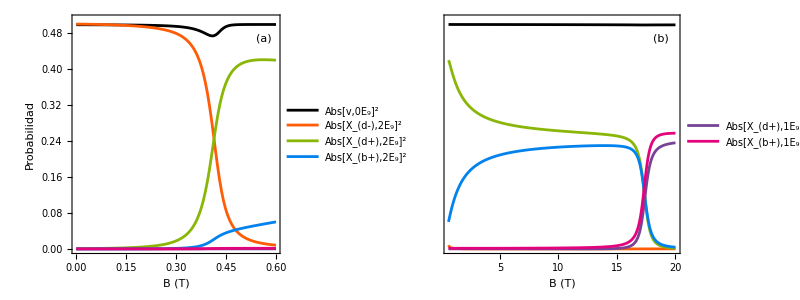
-Graphics-Configuración de Voigt (θ=0°)

```mathematica
Module[{n=5,θ=0,Δ,dat1,pt1,dat2,pt2,plot},
Δ[B_]:=Δ9[B,n];
dat1[i_]:=Table[{B,hfd[{9,i},Δ[B],B,θ,n]},{B,linspace[0.001,0.6,100]}];
pt1=ListLinePlot[{dat1[1],dat1[15],dat1[14],dat1[12],dat1[9],dat1[7]},PlotRange->{0,0.51},PlotStyle->COLORLIST,FrameLabel->{"B (T)","Probabilidad"},PlotLegends->legend[{Abs["v,0E_9"]^2,Abs["X_(d-),2E_9"]^2,Abs["X_(d+),2E_9"]^2,Abs["X_(b+),2E_9"]^2},{0.25,0.5},FontSize->12,LegendMarkerSize->12]];

dat2[i_]:=Table[{B,hfd[{9,i},Δ[B],B,θ,n]},{B,linspace[0.6,20,400]}];
pt2=ListLinePlot[{dat2[1],dat2[15],dat2[14],dat2[12],dat2[9],dat2[7]},PlotRange->{{0.6,20},{0,0.51}},PlotStyle->COLORLIST,FrameLabel->{"B (T)",None},FrameTicks->{{None,None},{Automatic,None}},PlotLegends->legend[{None,None,None,None,Abs["X_(d+),1E_9"]^2,Abs["X_(b+),1E_9"]^2},{0.45,0.8},LegendLayout->{"Row",1},FontSize->12,LegendMarkerSize->12]];
plot=Labeled[grid[{pt1,pt2}],Style["Configuración de Voigt (θ=0°)",18,FontFamily->"Times"],Top];
Export["Hopfield_θ0.pdf",plot];
plot
]//PrettyTiming
```

```mathematica
Clear[B9];
B9[n_]:=B9[n]=Module[{ϵ=10^-10,φ=(1+Sqrt[5])/2.0,f,Δx,x0,xf,h,x1,x2,θ=0},
f[B_]:=Abs[hfd[{9,15},Δ9[B,n],B,θ,n]-hfd[{9,14},Δ9[B,n],B,θ,n]];
Δx=0.05;
x0=0.412-Δx;
xf=0.412+Δx;
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[f[x1]>=f[x2],x0=x1,xf=x2];];(xf+x0)/2.0];
```

0h : 0m : 0s

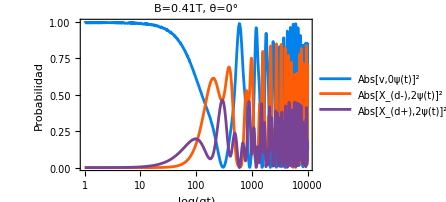

```mathematica
Module[{n=5,θ=0,Δ,B,datψ,ψ9ψ7B04θ0},
B=B9[n];
Δ=Δ9[B,n];
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ,B,θ,n][[i]]]^2},{t,logspace[0,4,800]}];
ψ9ψ7B04θ0=ListLogLinearPlot[{datψ[1],datψ[15],datψ[14]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,4,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->legend[{Abs["v,0ψ(t)"]^2,Abs["X_(d-),2ψ(t)"]^2,Abs["X_(d+),2ψ(t)"]^2},{0.24,0.46},FontSize->12,LegendMarkerSize->12],PlotLabel->Row[{"B=",NumberForm[B,2],"T, θ=",NumberForm[θ,2],"°"}],PlotStyle->{COLORLIST[[4]],COLORLIST[[2]],COLORLIST[[5]]}];
Export["ψ9ψ7_B0.4_θ0.pdf",ψ9ψ7B04θ0];
ψ9ψ7B04θ0
]//PrettyTiming
```

0h : 0m : 4s

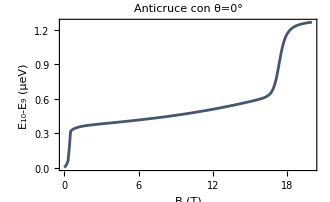
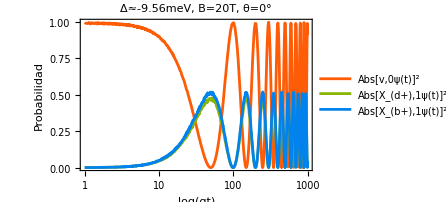
-Graphics- | -Graphics-

```mathematica
Module[{n=5,θ=0,Δ,Rabi9θ0,datψ,ψ9ψ7B20θ0},
Δ[B_]:=Δ9[B,n];
Rabi9θ0=ListPlot[Table[{B,ℰrest[9,Δ[B],B,θ,n]},{B,linspace[0.001,20,200]}],PlotRange->All,PlotStyle->COLORLIST[[7]],Joined->True,FrameLabel->{"B (T)","E_10-E_9 (μeV)"},PlotLabel->"Anticruce con θ=0°"];
Module[{B},B=20;
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ[B],B,θ,n][[i]]]^2},{t,logspace[0,3,600]}];
ψ9ψ7B20θ0=ListLogLinearPlot[{datψ[1],datψ[9],datψ[7]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,3,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->leyenda[{Abs["v,0ψ(t)"]^2,Abs["X_(d+),1ψ(t)"]^2,Abs["X_(b+),1ψ(t)"]^2}],PlotLabel->Row[{"Δ≈",NumberForm[Δ[B],3],"meV, B=",NumberForm[B,3],"T, θ=",θ,"°"}],PlotStyle->{COLORLIST[[2]],COLORLIST[[3]],COLORLIST[[4]]}];
];
Export["Rabi9θ0.pdf",Rabi9θ0];
Export["ψ9ψ7B20θ0.pdf",ψ9ψ7B20θ0];
Grid[{{Rabi9θ0,ψ9ψ7B20θ0}}]
]//PrettyTiming
```

## Configuración de Faraday

0h : 0m : 0s

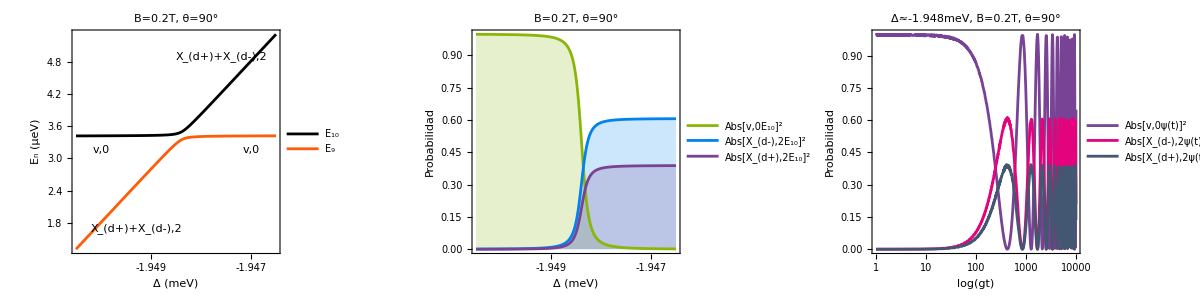

```mathematica
Module[{n=5,datψ,E10E9B02θ90,h10B02θ90,ψ15B02θ90,B=0.2,θ=π/2.0},
(*activacion de la nueva transicion*)
E10E9B02θ90=Plot[{ℰ[Δ,B,θ,n][[10]],ℰ[Δ,B,θ,n][[9]]},{Δ,-1.9505,-1.9465},PlotLegends->legend[{"E_10","E_9"},{0.15,0.77},FontSize->12,LegendMarkerSize->12],PlotStyle->COLORLIST,FrameLabel->{"Δ (meV)","E_n (μeV)"},FrameTicks->{{Automatic,None},{linticks[-1.951,-1.946,0.001],None}},
Epilog->{Inset["v,0",{-1.950,3.15}],Inset["v,0",{-1.947,3.15}],Inset["X_(d+)+X_(d-),2",{-1.9493,1.7}],Inset["X_(d+)+X_(d-),2",{-1.9476,4.90}]},PlotLabel->Row[{"B=",B,"T, θ=",NumberForm[Ceiling[θ*180/π],2],"°"}],PlotStyle->{COLORLIST[[1]],COLORLIST[[2]]}];
h10B02θ90=Plot[{hfd[{10,1},Δ,B,θ,n],hfd[{10,15},Δ,B,θ,n],hfd[{10,14},Δ,B,θ,n]},{Δ,-1.9505,-1.9465},FrameTicks->{{Automatic,None},{linticks[-1.951,-1.946,0.001],None}},PlotLegends->legend[{Abs["v,0E_10"]^2,Abs["X_(d-),2E_10"]^2,Abs["X_(d+),2E_10"]^2},{0.23,0.5},FontSize->12,LegendMarkerSize->12],FrameLabel->{"Δ (meV)","Probabilidad"},PlotLabel->Row[{"B=",B,"T, θ=",NumberForm[Ceiling[θ*180/π],2],"°"}],Filling->Bottom,PlotStyle->{COLORLIST[[3]],COLORLIST[[4]],COLORLIST[[5]]}];
Module[{Δ},Δ=-1.94839;
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ,B,θ,n][[i]]]^2},{t,logspace[0,4,800]}];
ψ15B02θ90=ListLogLinearPlot[{datψ[1],datψ[15],datψ[14]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,4,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->legend[{Abs["v,0ψ(t)"]^2,Abs["X_(d-),2ψ(t)"]^2,Abs["X_(d+),2ψ(t)"]^2},{0.25,0.5},FontSize->12,LegendMarkerSize->12],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",NumberForm[B,2],"T, θ=",NumberForm[Ceiling[θ*180/π],2],"°"}],PlotStyle->{COLORLIST[[5]],COLORLIST[[6]],COLORLIST[[7]]}];
];
Export["E10E9_B0.2_θ90.pdf",E10E9B02θ90];
Export["h10_B0.2_θ90.pdf",h10B02θ90];
Export["ψ15_B0.2_θ90.pdf",ψ15B02θ90];
Grid[{{E10E9B02θ90,h10B02θ90,ψ15B02θ90}}]//PrettyTiming
]
```

```mathematica
Module[{θ=π/2,n=5,auxdet,res,auxfit,res2,plot},
res[Δ_,B_]:=ℰrest[9,Δ,B,θ,n];
auxdet=DensityPlot[res[Δ,B],{B,0.001,20},{Δ,-1.8,-10.8},PlotLegends->Automatic,MaxRecursion->4,AspectRatio->1/2,FrameLabel->{"B (T)","Δ (meV)"},PlotLabel->"E_10-E_9(μeV) con θ=90°"];
auxfit=Plot[-1.95413+0.075B-0.0232 B^2,{B,0.001,20},PlotStyle->Dashed];
plot=rasta@Show[{auxdet,auxfit}];
Export["det_θ90.pdf",plot];
plot
]//PrettyTiming
```

0h : 0m : 1s

-Graphics-

```mathematica
Clear[Δ9θ90]
(*detuning para el cruce evitado*)
Δ9θ90[B_,n_]:=Module[{ϵ=10^-10,φ=(1+Sqrt[5])/2.0,f,g,Δx0,x0,xi,xf,h,x1,x2,θ=π/2},
g[Δ_,i_,j_]:=hfd[{i,1},Δ,B,θ,n]*hfd[{j,1},Δ,B,θ,n];
f[Δ_]:=-If[12.26<=B<=12.266,g[Δ,10,8],If[15.949<=B<=15.955,g[Δ,11,9],g[Δ,10,9]]];
x0=-1.95413+0.075B-0.0232 B^2;
Δx0=0.2;
xi=x0-Δx0;xf=x0+Δx0;
While[xf-xi>ϵ,h=(xf-xi)/φ;x1=xf-h;x2=xi+h;
If[f[x1]>=f[x2],xi=x1,xf=x2];];
x0=(xf+xi)/2.0
]
```

0h : 0m : 21s

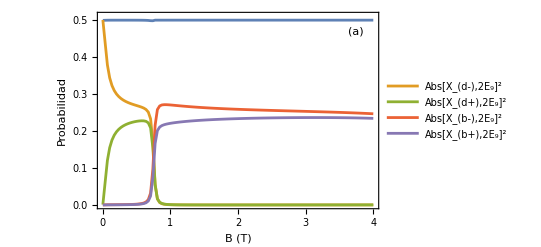
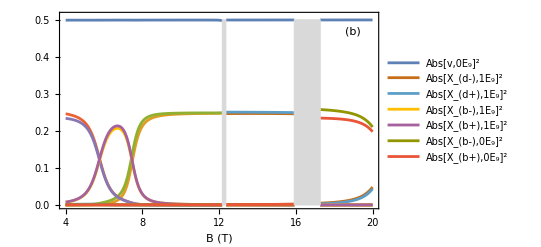
-Graphics- | -Graphics-Configuración de Faraday (θ=90°)

```mathematica
Module[{Δ,θ=π/2,n=5,dat1,dat2,aux1,aux2,dat3,aux3,f,rectangulo1,rectangulo2,plot},
Δ[B_]:=Δ9θ90[B,n];f[B_,i_]:=hfd[{9,i},Δ[B],B,θ,n];
dat1[i_]:=Table[{B,f[B,i]},{B,linspace[0.001,4,120]}];
aux1=ListLinePlot[Table[dat1[i],{i,{1,15,14,13,12}}],PlotRange->{0,0.51},FrameLabel->{"B (T)","Probabilidad"},PlotLegends->legend[{None,Abs["X_(d-),2E_9"]^2,Abs["X_(d+),2E_9"]^2,Abs["X_(b-),2E_9"]^2,Abs["X_(b+),2E_9"]^2},{0.5,0.75},FontSize->12,LegendMarkerSize->12,LegendLayout->{"Row",2}]];
dat2[i_]:=Table[{B,Piecewise[{{f[B,i],0<B<12.17},{f[B,i],12.35<B<=15.94},{f[B,i],B==15.96},{f[B,i],17.26<=B<=20}},None]},{B,linspace[4,20,680]}];
aux2=ListLinePlot[Table[dat2[i],{i,{1,15,14,13,12,10,9,8,7,3,2}}],PlotRange->{{4,20},{0,0.51}},FrameLabel->{"B (T)",None},PlotLegends->LineLegend[Automatic,{Abs["v,0E_9"]^2,None,None,None,None,Abs["X_(d-),1E_9"]^2,Abs["X_(d+),1E_9"]^2,Abs["X_(b-),1E_9"]^2,Abs["X_(b+),1E_9"]^2,Abs["X_(b-),0E_9"]^2,Abs["X_(b+),0E_9"]^2},LabelStyle->{FontFamily->"Times",FontSize->12},LegendLayout->{"Column",1},LegendMarkerSize->{12,2},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray,Background->Lighter[Gray,0.9]]&)]];
rectangulo1=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{12.17,0},{12.35,0.5}]}];
rectangulo2=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{15.92,0},{17.27,0.5}]}];
plot=Labeled[grid[{aux1,Show[{aux2,rectangulo1,rectangulo2}]}],Style["Configuración de Faraday (θ=90°)",18,FontFamily->"Times"],Top];
Export["Hopfield_θ90.pdf",plot];
plot
]//PrettyTiming
```

```mathematica
Clear[B9θ90];
B9θ90[n_]:=B9θ90[n]=Module[{ϵ=10^-10,φ=(1+Sqrt[5])/2.0,f,Δx,x0,xf,h,x1,x2,θ=π/2},
f[B_]:=Abs[hfd[{9,15},Δ9θ90[B,n],B,θ,n]-hfd[{9,13},Δ9θ90[B,n],B,θ,n]];
Δx=0.05;
x0=0.710-Δx;
xf=0.785+Δx;
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[f[x1]>=f[x2],x0=x1,xf=x2];];(xf+x0)/2.0];
```

0h : 0m : 9s

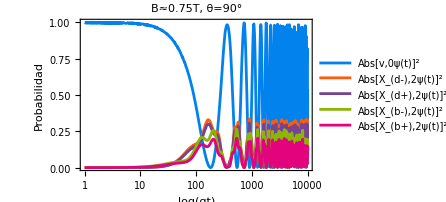

```mathematica
Module[{n=5,θ=π/2,Δ,B,datψ,ψ9ψ7B075θ90},
B=B9θ90[n];
Δ=Δ9θ90[B,n];
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ,B,θ,n][[i]]]^2},{t,logspace[0,4,800]}];
ψ9ψ7B075θ90=ListLogLinearPlot[{datψ[1],datψ[15],datψ[14],datψ[13],datψ[12]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,4,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->leyenda[{Abs["v,0ψ(t)"]^2,Abs["X_(d-),2ψ(t)"]^2,Abs["X_(d+),2ψ(t)"]^2,Abs["X_(b-),2ψ(t)"]^2,Abs["X_(b+),2ψ(t)"]^2}],PlotLabel->Row[{"B≈",NumberForm[B,3],"T, θ=90°"}],PlotStyle->{COLORLIST[[4]],COLORLIST[[2]],COLORLIST[[5]],COLORLIST[[3]],COLORLIST[[6]]}];
Export["ψ9ψ7_B0.75_θ90.pdf",ψ9ψ7B075θ90];
ψ9ψ7B075θ90
]//PrettyTiming
```

0h : 0m : 29s

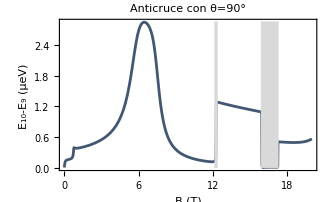
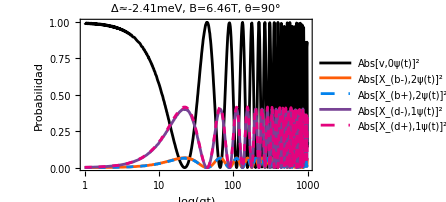
-Graphics- | -Graphics-

```mathematica
Module[{n=5,θ=π/2,Δ,Rabi9θ90P1,Rabi9θ90,datψ,ψ9ψ7B646θ90,rectangulo1,rectangulo2},
Δ[B_]:=Δ9θ90[B,n];
Rabi9θ90P1=ListPlot[Table[{B,ℰrest[9,Δ[B],B,θ,n]},{B,linspace[0.001,20,1200]}],PlotRange->All,PlotStyle->COLORLIST[[7]],Joined->True,FrameLabel->{"B (T)","E_10-E_9 (μeV)"},PlotLabel->"Anticruce con θ=90°"];
Module[{B},B=6.46;
datψ[i_]:=Table[{t,Abs[ψ[t/gbb,Δ[B],B,θ,n][[i]]]^2},{t,logspace[0,3,600]}];
ψ9ψ7B646θ90=ListLogLinearPlot[{datψ[1],datψ[13],datψ[12],datψ[8],datψ[7]},Joined->True,FrameTicks->{{Automatic,None},{logticks[0,3,1],None}},FrameLabel->{"log(gt)","Probabilidad"},PlotLegends->leyenda[{Abs["v,0ψ(t)"]^2,Abs["X_(b-),2ψ(t)"]^2,Abs["X_(b+),2ψ(t)"]^2,Abs["X_(d-),1ψ(t)"]^2,Abs["X_(d+),1ψ(t)"]^2}],PlotLabel->Row[{"Δ≈",NumberForm[Δ[B],3],"meV, B=",NumberForm[B,3],"T, θ=90°"}],PlotStyle->{COLORLIST[[1]],COLORLIST[[2]],{Dashed,COLORLIST[[4]]},COLORLIST[[5]],{Dashed,COLORLIST[[6]]}}];
];
rectangulo1=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{12.17,0},{12.35,2.85}]}];
rectangulo2=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{15.92,0},{17.27,2.85}]}];
Rabi9θ90=Show[Rabi9θ90P1,rectangulo1,rectangulo2];
Export["Rabi9_θ90.pdf",Rabi9θ90];
Export["ψ9ψ7_B6.46_θ90.pdf",ψ9ψ7B646θ90];
Grid[{{Rabi9θ90,ψ9ψ7B646θ90}}]
]//PrettyTiming
```

# Hamiltoniano interactuando con el entorno

```mathematica
(*parametros disipativos*)
{κ=7.89*10^-4,γb=1.87*10^-5,γd=0.1γb,γϕ=4.0*10^-4};
```

```mathematica
(*sistema cuantico abierto*)
Clear[cops,ℒ,ρss,Nph,g2,gb2]
cops[n_]:=cops[n]=Join[{√κ c[n]},√γb Table[σ[0,j,n],{j,2}],√γd Table[σ[0,j,n],{j,3,4}],√γϕ Table[σ[j,j,n],{j,4}]];
ℒ[Δ_,B_,θ_,n_]:=ℒ[Δ,B,θ,n]=Liouvillian[H[Δ,B,θ,n],cops[n]]
ρss[Δ_,B_,θ_,n_]:=ρss[Δ,B,θ,n]=Chop[SteadyState[ℒ[Δ,B,θ,n]]]
Nph[Δ_,B_,θ_,n_]:=Nph[Δ,B,θ,n]=
Chop[Tr[c[n]ᵀ.c[n].ρss[Δ,B,θ,n]]]
g2[Δ_,B_,θ_,n_]:=g2[Δ,B,θ,n]=
Chop[Tr[MatrixPower[c[n]ᵀ,2].MatrixPower[c[n],2].ρss[Δ,B,θ,n]]/Tr[c[n]ᵀ.c[n].ρss[Δ,B,θ,n]]^2]
gb2[Δ_,B_,θ_,n_]:=gb2[Δ,B,θ,n]=
Chop[Tr[MatrixPower[c[n]ᵀ,4].MatrixPower[c[n],4].ρss[Δ,B,θ,n]]/Tr[MatrixPower[c[n]ᵀ,2].MatrixPower[c[n],2].ρss[Δ,B,θ,n]]^2]
ee[ωs_,Δ_,B_,θ_,n_]:=ee[ωs,Δ,B,θ,n]=
EmissionSpectrum[ρss[Δ,B,θ,n],ωs,ℒ[Δ,B,θ,n],c[n]]
```

```mathematica
ρ0[n_]:=SparseArray[{{1,1}->1,{i_,j_}->0},{Length[c[n]],Length[c[n]]}];
Clear[pop]
pop[ρ0_,ti_,tf_,dt_,Δ_,B_,θ_,n_]:=pop[ρ0,ti,tf,dt,Δ,B,θ,n]=Module[{superop,rho0,m,P,times0,pops,t,rho},
superop=ℒ[Δ,B,θ,n];
P=MatrixExp[superop*dt]//Chop;(*Define the propagator*)
{times0,pops}={{},{}};(*Allocate sets*)
{t,rho}={ti,ρ0};(*Initialise*)
(*propagate*)
Do[
AppendTo[pops,rho//Chop];
(*Append current time*)
AppendTo[times0,t];
(*Propagate time and state*)
{t,rho}={t+dt,Unvec[P.Vec[rho]]},
{Ceiling[tf/dt]}
];
{times0,pops}
]
```

## Vladimir

0h : 0m : 0s

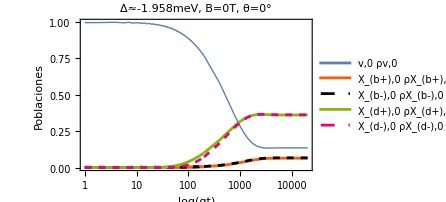

```mathematica
Module[{n=5,ti,tf,dt,Δ=-1.9576,B=0,θ=0,ts,rhoP1,rhoP2,dat,ρB0P1,ρB0P2,ρB0},
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB0P1=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",B,"T, θ=",θ,"°"}]];
ti=10^4;tf=10^6;dt=tf*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB0P2=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},FrameLabel->{"log(t)","Poblaciones"},PlotLegends->leyenda[{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0"}]];
ρB0=Show[{ρB0P1,ρB0P2},PlotRange->All];
Export["ρB0.pdf",ρB0];
ρB0
]//PrettyTiming
```

## Configuración de Voigt

0h : 1m : 4s

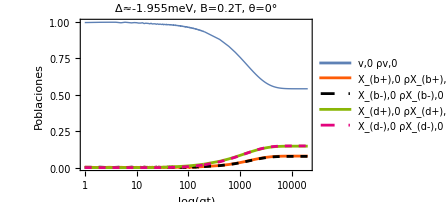
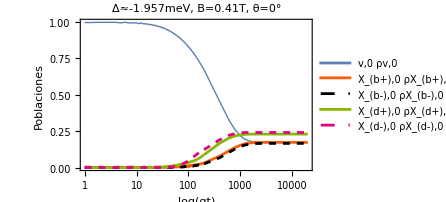
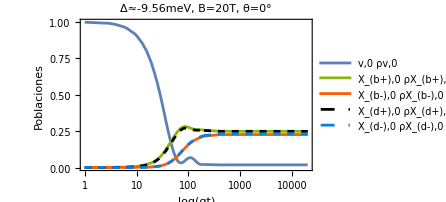
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Module[{n=5,ti,tf,dt,B,θ=0,Δ,ts,rhoP1,rhoP2,dat,ρB02θ0P1,ρB02θ0P2,ρB02θ0,ρB04θ0P1,ρB04θ0P2,ρB04θ0,ρB20θ0P1,ρB20θ0P2,ρB20θ0},
B=0.2;Δ=Δ9[B,n];
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB02θ0P1=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",B,"T, θ=",θ,"°"}]];
ti=10^4;tf=10^6;dt=tf*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB02θ0P2=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},PlotLegends->legend[{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0"},{0.25,0.5},FontSize->12,LegendMarkerSize->12]];
ρB02θ0=Show[{ρB02θ0P1,ρB02θ0P2},PlotRange->All];

B=B9[n];Δ=Δ9[B,n];
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB04θ0P1=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",NumberForm[B,2],"T, θ=",θ,"°"}]];
ti=10^4;tf=10^6;dt=tf*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB04θ0P2=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},PlotLegends->leyenda[{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0"}]];
ρB04θ0=Show[{ρB04θ0P1,ρB04θ0P2},PlotRange->All];

B=20;Δ=Δ9[B,n];
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB20θ0P1=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[3]],COLORLIST[[2]],{COLORLIST[[1]],Dashed},{COLORLIST[[4]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",NumberForm[B,2],"T, θ=",θ,"°"}]];
ti=10^4;tf=10^6;dt=tf*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB20θ0P2=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[3]],COLORLIST[[2]],{COLORLIST[[1]],Dashed},{COLORLIST[[4]],Dashed}},
PlotLegends->LineLegend[Automatic,{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0"},LabelStyle->{FontFamily->"Times",FontSize->12},LegendLayout->{"Column",1},LegendMarkerSize->{12,2},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray,Background->Lighter[Gray,0.9]]&)]];
ρB20θ0=Show[{ρB20θ0P1,ρB20θ0P2},PlotRange->All];

Export["ρ_B0.2_θ0.pdf",ρB02θ0];
Export["ρ_B0.4_θ0.pdf",ρB04θ0];
Export["ρ_B20_θ0.pdf",ρB20θ0];
Grid[{{ρB02θ0,ρB04θ0},{ρB20θ0}}]
]//PrettyTiming
```

0h : 0m : 25s

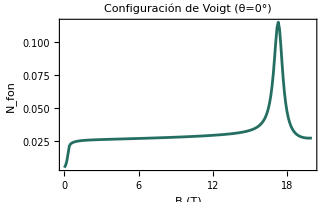

```mathematica
Module[{Δ,θ=0,n=5,plt},Δ[B_]:=Δ9[B,n];
plt=ListPlot[Table[{B,Nph[Δ[B],B,θ,n]},{B,linspace[0.001,20,200]}],PlotRange->All,FrameLabel->{"B (T)","N_fon"},Joined->True,PlotStyle->COLORLIST[[9]],PlotLabel->Style["Configuración de Voigt (θ=0°)",18,FontFamily->"Times"]];
Export["Nfon_θ0.pdf",plt];
plt
]//PrettyTiming
```

0h : 0m : 17s

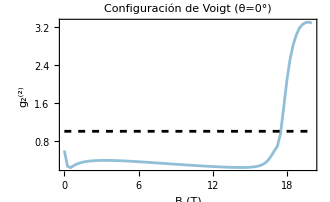

```mathematica
Module[{Δ,θ=0,n=6,plt},
Δ[B_]:=Δ9[B,n];
plt=ListPlot[{Table[{B,gb2[Δ[B],B,θ,n]},{B,linspace[0.001,20,80]}],Table[{B,1},{B,linspace[0,20,2]}]},PlotRange->All,FrameLabel->{"B (T)","g_2^(2)"},Joined->True,PlotStyle->{COLORLIST[[10]],{Black,Dashed}},PlotLabel->Style["Configuración de Voigt (θ=0°)",18,FontFamily->"Times"]];
Export["gb2_θ0.pdf",plt];
plt
]//PrettyTiming
```

```mathematica
Clear[mingb2];
mingb2[n_]:=mingb2[n]=Module[{ϵ=10^-8,φ=(1+Sqrt[5])/2.0,f,Δx,x0,xf,h,x1,x2,θ=0,Δ},
Δ[B_]:=Δ9[B,n];
f[B_]:=gb2[Δ[B],B,θ,n];
Δx=0.05;
x0=0.38-Δx;
xf=0.38+Δx;
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[f[x1]>=f[x2],x0=x1,xf=x2];];(xf+x0)/2.0];
```

0h : 0m : 0s

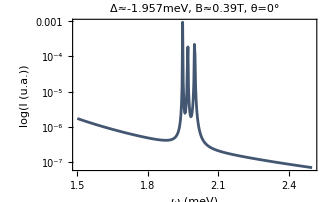

```mathematica
Module[{Δ,θ=0,n=7,B,ωs,plt},
B=mingb2[n];
Δ[B_]:=Δ9[B,n];
ωs=linspace[1.5,2.5,400];
plt=ListLogPlot[{ωs,Abs@ee[ωs,Δ[B],B,θ,n]}ᵀ,PlotRange->All,FrameLabel->{"ω (meV)",Log["I (u.a.)"]},Joined->True,PlotStyle->COLORLIST[[7]],FrameTicks->{{logticks[-7,-3,1],None},{Automatic,None}},PlotLabel->Row[{"Δ≈",NumberForm[Δ[B],4],"meV, B≈",NumberForm[B,2],"T, θ=0°"}]];
Export["ee_Δ-1.957_B0.39_θ0.pdf",plt];
plt
]//PrettyTiming
```

## Configuración de Faraday

0h : 1m : 14s

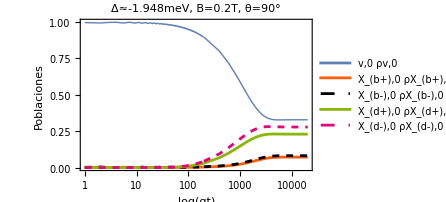
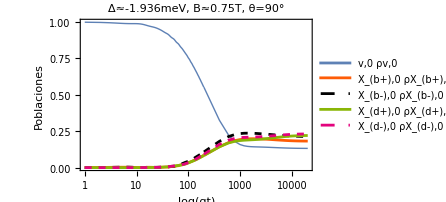
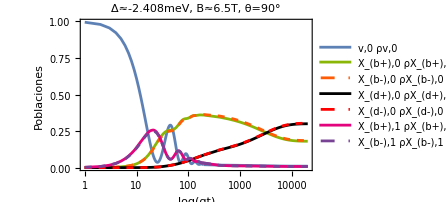
-Graphics- | -Graphics- | -Graphics-

```mathematica
Module[{n=5,ti,tf,dt,B,θ=π/2,Δ,ts,rho,rhoP1,rhoP2,dat,ρB02θ90P1,ρB02θ90P2,ρB02θ90,ρB08θ90P1,ρB08θ90P2,ρB08θ90,ρB6θ90P1,ρB6θ90P2,ρB6θ90},
B=0.2;Δ=Δ9θ90[B,n];
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB02θ90P1=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",B,"T, θ=90°"}]];
ti=10^4;tf=10^6;dt=(tf-ti)*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB02θ90P2=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},PlotLegends->legend[{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0"},{0.25,0.5},FontSize->12,LegendMarkerSize->12],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B=",B,"T, θ=90°"}]];
ρB02θ90=Show[{ρB02θ90P1,ρB02θ90P2},PlotRange->All];

B=B9θ90[n];Δ=Δ9θ90[B,n];
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB08θ90P1=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B≈",NumberForm[B,2],"T, θ=90°"}]];
ti=10^4;tf=10^6;dt=(tf-ti)*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB08θ90P2=ListLogLinearPlot[Table[dat[i],{i,5}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[2]],{COLORLIST[[1]],Dashed},COLORLIST[[3]],{COLORLIST[[6]],Dashed}},PlotLegends->leyenda[{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0"}],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B≈",NumberForm[B,2],"T, θ=90°"}]];
ρB08θ90=Show[{ρB08θ90P1,ρB08θ90P2},PlotRange->All];

B=6.46;Δ=Δ9θ90[B,n];
ti=0;tf=10^4;dt=tf*0.005;{ts,rhoP1}=pop[ρ0[n],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP1[[All,i,i]]}ᵀ;
ρB6θ90P1=ListLogLinearPlot[Table[dat[i],{i,{1,2,3,4,5,7,8}}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[3]],{COLORLIST[[2]],Dashed},COLORLIST[[1]],{Red,Dashed},COLORLIST[[6]],{COLORLIST[[5]],Dashed}},FrameLabel->{"log(gt)","Poblaciones"},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B≈",NumberForm[B,2],"T, θ=90°"}]];
ti=10^4;tf=10^6;dt=(tf-ti)*0.01;{ts,rhoP2}=pop[rhoP1[[-1]],ti,tf,dt,Δ,B,θ,n];dat[i_]:={ts*gbb,rhoP2[[All,i,i]]}ᵀ;
ρB6θ90P2=ListLogLinearPlot[Table[dat[i],{i,{1,2,3,4,5,7,8}}],Joined->True,PlotRange->{0,1},FrameTicks->{{Automatic,None},{logticks[0,6,1],None}},PlotStyle->{Thick,COLORLIST[[3]],{COLORLIST[[2]],Dashed},COLORLIST[[1]],{Red,Dashed},COLORLIST[[6]],{COLORLIST[[5]],Dashed}},
PlotLegends->LineLegend[Automatic,{"v,0 ρv,0","X_(b+),0 ρX_(b+),0","X_(b-),0 ρX_(b-),0","X_(d+),0 ρX_(d+),0","X_(d-),0 ρX_(d-),0","X_(b+),1 ρX_(b+),1","X_(b-),1 ρX_(b-),1"},LabelStyle->{FontFamily->"Times",FontSize->12},LegendLayout->{"Column",1},LegendMarkerSize->{12,2},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray,Background->Lighter[Gray,0.9]]&)],PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B≈",NumberForm[B,2],"T, θ=90°"}]];
ρB6θ90=Show[{ρB6θ90P1,ρB6θ90P2},PlotRange->All];

Export["ρ_B0.2_θ90.pdf",ρB02θ90];
Export["ρ_B0.75_θ90.pdf",ρB08θ90];
Export["ρ_B6.5_θ90.pdf",ρB6θ90];

Grid[{{ρB02θ90,ρB08θ90,ρB6θ90}}]
]//PrettyTiming
```

0h : 0m : 27s

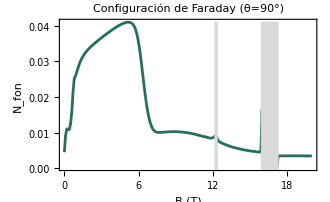

```mathematica
Module[{Δ,θ=π/2,n=5,rectangulo1,rectangulo2,plt},Δ[B_]:=Δ9θ90[B,n];
rectangulo1=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{12.17,-3},{12.35,0.041}]}];
rectangulo2=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{15.92,-3},{17.27,0.041}]}];
plt=Show[{ListPlot[Table[{B,Nph[Δ[B],B,θ,n]},{B,linspace[0.001,20,200]}],PlotRange->All,FrameLabel->{"B (T)","N_fon"},Joined->True,PlotStyle->COLORLIST[[9]],PlotLabel->Style["Configuración de Faraday (θ=90°)",18,FontFamily->"Times"]],rectangulo1,rectangulo2}];
Export["Nfon_θ90.pdf",plt];
plt
]//PrettyTiming
```

0h : 0m : 0s

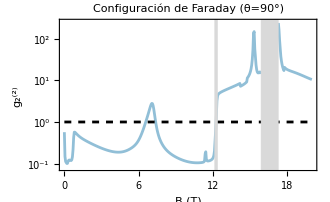

```mathematica
Module[{Δ,θ=π/2,n=5,Bmax=20,rectangulo1,rectangulo2,f,plt},
Δ[B_]:=Δ9θ90[B,n];
rectangulo1=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{12.17,-3},{12.35,186}]}];
rectangulo2=Graphics[{LightGray,EdgeForm[Dashed],Rectangle[{15.92,-3},{17.27,186}]}];
f[B_]:=Piecewise[{{None,12.25<B<12.27},{None,15.92<B<17.27}},gb2[Δ[B],B,θ,n]];
plt=Show[{ListPlot[{Table[{B,f[B]},{B,linspace[0.001,Bmax,400]}],Table[{B,1},{B,linspace[0.001,Bmax,3]}]},FrameLabel->{"B (T)","g_2^(2)"},Joined->True,PlotStyle->{COLORLIST[[10]],{Black,Dashed}},PlotLabel->Style["Configuración de Faraday (θ=90°)",18,FontFamily->"Times"],ScalingFunctions->"Log",PlotRange->{0.08,250},FrameTicks->{{logticks[-1,2,1],None},{Automatic,None}}],rectangulo1,rectangulo2}];
Export["gb2_θ90.pdf",plt];
plt
]//PrettyTiming
```

```mathematica
Clear[mingb2θ90];
mingb2θ90[n_]:=mingb2θ90[n]=Module[{ϵ=10^-8,φ=(1+Sqrt[5])/2.0,f,Δx,x0,xf,h,x1,x2,θ=π/2,Δ},
Δ[B_]:=Δ9θ90[B,n];
f[B_]:=gb2[Δ[B],B,θ,n];
Δx=0.5;
x0=10.5-Δx;
xf=10.5+Δx;
While[xf-x0>ϵ,h=(xf-x0)/φ;x1=xf-h;x2=x0+h;
If[f[x1]>=f[x2],x0=x1,xf=x2];];(xf+x0)/2.0];
```

0h : 0m : 18s

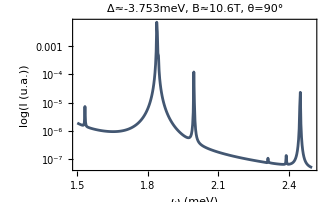

```mathematica
Module[{Δ,θ=π/2,n=6,B,ωs,plt},
B=mingb2θ90[n];
Δ=Δ9θ90[B,n];
ωs=linspace[1.5,2.5,400];
plt=ListLogPlot[{ωs,ee[ωs,Δ,B,θ,n]}ᵀ,PlotRange->All,FrameLabel->{"ω (meV)",Log["I (u.a.)"]},Joined->True,PlotStyle->COLORLIST[[7]],FrameTicks->{{logticks[-7,-2,1],None},{Automatic,None}},PlotLabel->Row[{"Δ≈",NumberForm[Δ,4],"meV, B≈",NumberForm[B,3],"T, θ=90°"}]];
Export["ee_Δ-3.75_B10.6_θ90.pdf",plt];
plt
]//PrettyTiming
```